```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
rho[λ_] := 1/($N √(2π))Exp[-λ^2/2]Sum[1/(2^j j!)HermiteH[j, λ/(√2)]^2, {j, 0, $N-1}];
```

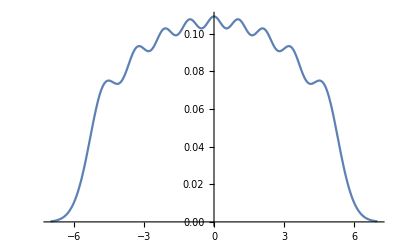

```mathematica
plt = Plot[rho[λ], {λ, -7, 7}]
```

```mathematica
mats = RandomVariate[GaussianUnitaryMatrixDistribution[$N], 100000];
```

```mathematica
eig = Flatten[Eigenvalues/@mats];
```

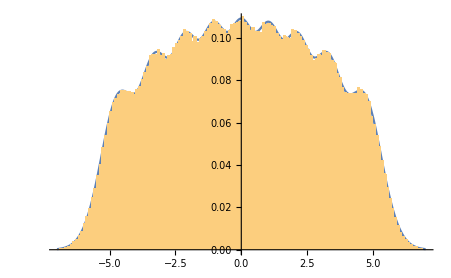

```mathematica
Show[plt, Histogram[eig, 200, PDF]]
```

```mathematica
($N)/(√(2π))Integrate[rho[b]Exp[-(($N)^2(λ-b)^2)/2], {t, -∞, ∞}]
```

(9 ⅇ^(-(81 λ^2)/164) (5121578592424634621915948634476800+6561 λ^2 (69081614122884933743318656000+2187 λ^2 (391066207233737747700181760+6561 λ^2 (-46728361890285276750080+6561 λ^2 (2943262130732711200+2187 λ^2 (-270684569906240+6561 λ^2 (4378265360+6561 λ^2 (-34768+729 λ^2)))))))))/(18719733088101707512022186831380480 √82)

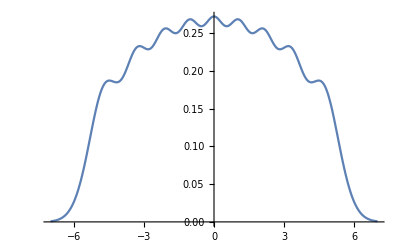

```mathematica
plt = Plot[%, {λ, -7, 7}]
```